```mathematica
Clear["Global`*"]
```

# Model Planet-Moon (v1.2)

```mathematica
thisfolder=NotebookDirectory[]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/

### Get Linear Ephemeris

```mathematica
LRVplan=Import[StringJoin[thisfolder,"LRVplan-stats.dat"],"Table"];
MAPplan=LRVplan[[First[First[Position[LRVplan,{"MAP","Parameters"}]]]+2;;All]];nparamorig=Last[MAPplan][[1]];
```

```mathematica
Pglob=MAPplan[[4]][[2]]
τglob=MAPplan[[5]][[2]]
```

160.88447521950783

55110.504753999398

### Get Transit Times

```mathematica
data1=Import[StringJoin[thisfolder,"TTVplan-post_equal_weights.dat"],"Table"];
sdim1=Last[Dimensions[data1]]-1
Dimensions[data1]
```

16

{37783,17}

```mathematica
j=0;k=0;Label[jloop];j=j+1;k=k+1;Subscript[τtab, k]=data1[[All,nparamorig+j]];If[nparamorig+j<sdim1,Goto[jloop]];
nepochs=k
```

9

### Get Mazeh Times

```mathematica
mazehdatabase=Import[StringJoin["/Users/",StringSplit[NotebookDirectory[],"/"][[2]],"/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/mazeh_analysis/ttvs.txt"],"Table"];
```

```mathematica
temp=StringSplit[thisfolder,"/"];
mazehsub=Select[mazehdatabase,#[[1]]==ToExpression[StringSplit[temp[[Length[temp]-1]],"-"][[2]]]&];
```

```mathematica
timesM=Table[{mazehsub[[i,2]],54900+mazehsub[[i,3]]+mazehsub[[i,4]]/(24*60),mazehsub[[i,5]]/(24*60)},{i,1,Length[mazehsub]}];
"adjust epoch numbers...";
timesM=Sort[Table[{Round[(timesM[[j,2]]-τglob)/Pglob],timesM[[j,2]],timesM[[j,3]],timesM[[j,3]]},{j,1,Length[timesM]}]];
```

### Format times and TTVs

```mathematica
timesK=Sort[Table[{Round[(Median[Subscript[τtab, j]]-τglob)/Pglob],Median[Subscript[τtab, j]],Median[Subscript[τtab, j]]-Quantile[Subscript[τtab, j],0.5-0.5Erf[1/√2]],Quantile[Subscript[τtab, j],0.5+0.5Erf[1/√2]]-Median[Subscript[τtab, j]]},{j,1,nepochs}]];
```

```mathematica
"M is weirdly offset from K, try fixing...";
timesE=Drop[Union[timesM[[All,1]],timesK[[All,1]]],{3}]
tempM=Sort[Select[timesM,MemberQ[timesE,#[[1]]]&]];
tempK=Sort[Select[timesK,MemberQ[timesE,#[[1]]]&]];
tempfn[α_]:=Sum[((tempM[[i,2]]-α)-tempK[[i,2]])^2/(Mean[{tempK[[i,3]],tempK[[i,4]]}]^2+Mean[{tempM[[i,3]],tempM[[i,4]]}]^2),{i,1,Length[timesE]}];
αoffset=Last[Last[Last[NMinimize[tempfn[α],α]]]]
timesM=Table[{timesM[[i,1]],timesM[[i,2]]-αoffset,timesM[[i,3]],timesM[[i,4]]},{i,1,Length[timesM]}];
```

{0,1,3,4,5,6,7,8}

0.00449768

```mathematica
rawTTVsM=Table[{timesM[[i,1]],timesM[[i,2]],24*60(timesM[[i,2]]-timesM[[i,1]] Pglob-τglob),24*60timesM[[i,3]],24*60timesM[[i,4]]},{i,1,Length[timesM]}];
rawTTVsK=Table[{timesK[[i,1]],timesK[[i,2]],24*60(timesK[[i,2]]-timesK[[i,1]] Pglob-τglob),24*60timesK[[i,3]],24*60timesK[[i,4]]},{i,1,Length[timesK]}];
```

```mathematica
"Estimate maximum expected level of scatter";
κM=StandardDeviation[rawTTVsM[[All,3]]]
σrescaleM=√(StandardDeviation[rawTTVsM[[All,3]]]/√(Sum[(rawTTVsM[[i,4]])^2,{i,1,Length[rawTTVsM]}]/Length[rawTTVsM]));
ΥM=1/(√(2(Length[rawTTVsM]-1)))√(Sum[(σrescaleM rawTTVsM[[i,4]])^4,{i,1,Length[rawTTVsM]}]/Sum[(σrescaleM rawTTVsM[[i,4]])^2,{i,1,Length[rawTTVsM]}])
extremeM=κM+5ΥM
```

5.45319

0.481512

7.86075

```mathematica
"flag any TTVs from K for which the measurement is outside the extreme value (unreliable), or both errors exceed that level (not useful)";
badepochsK=Select[rawTTVsK,((#[[4]]>extremeM)&&(#[[5]]>extremeM))&][[All,1]]
Length[badepochsK]
badepochsM=Select[rawTTVsM,((#[[4]]>extremeM)&&(#[[5]]>extremeM))&][[All,1]]
Length[badepochsM]
```

{}

0

{}

0

```mathematica
"remove bad epochs";
TTVsK=Select[rawTTVsK,!MemberQ[badepochsK,#[[1]]]&];
TTVsM=Select[rawTTVsM,!MemberQ[badepochsM,#[[1]]]&];
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
offset=0.05;
Kplot=Table[{{TTVsK[[i,1]]-offset,TTVsK[[i,3]]},ErrorBar[{-TTVsK[[i,4]],TTVsK[[i,5]]}]},{i,1,Length[TTVsK]}];
Mplot=Table[{{TTVsM[[i,1]]+offset,TTVsM[[i,3]]},ErrorBar[{-TTVsM[[i,4]],TTVsM[[i,5]]}]},{i,1,Length[TTVsM]}];
```

```mathematica
buffer=0.1;{Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-0.5buffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]),Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]+0.5buffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]])}
```

{-0.4,8.4}

9.73353

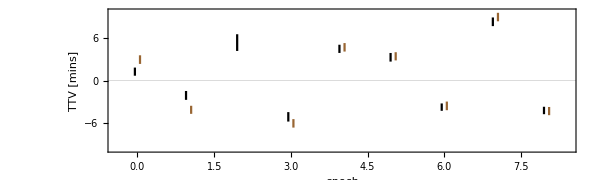

```mathematica
ybuffer=1.25;
yrange=Max[Max[-Min[TTVsK[[All,3]]-ybuffer TTVsK[[All,4]]],Max[TTVsK[[All,3]]+ybuffer TTVsK[[All,5]]]],
Max[-Min[TTVsM[[All,3]]-ybuffer TTVsM[[All,4]]],Max[TTVsM[[All,3]]+ybuffer TTVsM[[All,5]]]]]
xbuffer=0.1;xrange={Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-0.5xbuffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]),Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]+0.5xbuffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]])};
ttvplotK=ErrorListPlot[Kplot,Frame->True,Axes->None,PlotRange->{xrange,{-yrange,yrange}},GridLines->{{},{0}},AspectRatio->0.3,ImageSize->{600,Automatic},FrameLabel->{"epoch","TTV [mins]"},BaseStyle->{FontFamily->"CMU Serif",FontSize->24},PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing;
ttvplotM=ErrorListPlot[Mplot,Frame->True,Axes->None,PlotRange->{xrange,{-yrange,yrange}},GridLines->{{},{0}},AspectRatio->0.3,ImageSize->{600,Automatic},FrameLabel->{"epoch","TTV [mins]"},BaseStyle->{FontFamily->"CMU Serif",FontSize->24},PlotStyle->Brown,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing;
dataplot=Show[ttvplotM,ttvplotK]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"TTVs_sym.dat"],Table[{TTVsK[[i,1]],TTVsK[[i,2]],0.5(TTVsK[[i,4]]+TTVsK[[i,5]])/1440},{i,1,Length[TTVsK]}],"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/TTVs_sym.dat

```mathematica
Export[StringJoin[NotebookDirectory[],"TTVsK.dat"],TTVsK,"Table"]
Export[StringJoin[NotebookDirectory[],"TTVsM.dat"],TTVsM,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/TTVsK.dat

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/TTVsM.dat

### LATEX table

```mathematica
timey=Table[{TTVsK[[i,1]],TTVsK[[i,2]]-55000,N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440],TTVsK[[i,3]],TTVsK[[i,4]],TTVsK[[i,5]]},{i,1,Length[TTVsK]}];
j=0;Label[jloop];j=j+1;dp=Length[Characters[ToString[N[Min[timey[[j,3]],timey[[j,4]]],2]]]]-5;rp=Length[Characters[ToString[Round[timey[[j,2]]]]]];dpx=Length[Characters[ToString[N[Min[timey[[j,6]],timey[[j,7]]],2]]]]-2;rpx=Length[Characters[ToString[Round[timey[[j,5]]]]]];Subscript[α, j]={timey[[j,1]],ToString[N[Round[timey[[j,2]],10^(-dp)],dp+rp+0]],ToString[N[Round[timey[[j,3]],10^(-dp)],dp-2]],ToString[N[Round[timey[[j,4]],10^(-dp)],dp-2]]};Subscript[β, j]={ToString[N[Round[timey[[j,5]],10^(-dpx)],dpx+1]],ToString[N[Round[timey[[j,6]],10^(-dpx)],dpx+1]],ToString[N[Round[timey[[j,7]],10^(-dpx)],dpx+1]]};If[j<Length[timey],Goto[jloop]];
tabby=Table[{Subscript[α, j][[1]],Subscript[α, j][[2]],Subscript[α, j][[3]],Subscript[α, j][[4]],Subscript[β, j][[1]],Subscript[β, j][[2]],Subscript[β, j][[3]]},{j,1,Length[timey]}];
tabby=Table[StringJoin["$",ToString[Subscript[α, j][[1]]],"$ & $",Subscript[α, j][[2]],"_{-",Subscript[α, j][[3]],"}^{+",Subscript[α, j][[4]],"}$ & $",Subscript[β, j][[1]],"_{-",Subscript[β, j][[2]],"}^{+",Subscript[β, j][[3]],"}$"],{j,1,Length[timey]}]
```

{$0$ & $110.50563_{-0.000400}^{+0.000400}$ & $1.26_{-0.580}^{+0.570}$,$1$ & $271.387770_{-0.0004370}^{+0.0004330}$ & $-2.10_{-0.630}^{+0.620}$,$2$ & $432.277439_{-0.0008260}^{+0.0008150}$ & $5.4_{-1.2}^{+1.2}$,$3$ & $593.154621_{-0.0004710}^{+0.0004570}$ & $-5.12_{-0.680}^{+0.660}$,$4$ & $754.045764_{-0.0003960}^{+0.0004090}$ & $4.48_{-0.570}^{+0.590}$,$5$ & $914.929416_{-0.0004220}^{+0.0004240}$ & $3.29_{-0.610}^{+0.610}$,$6$ & $1075.80899_{-0.000360}^{+0.000360}$ & $-3.76_{-0.520}^{+0.520}$,$7$ & $1236.70185_{-0.000420}^{+0.000430}$ & $8.31_{-0.610}^{+0.610}$,$8$ & $1397.577617_{-0.0003660}^{+0.0003630}$ & $-4.23_{-0.530}^{+0.520}$}

```mathematica
Export[StringJoin[thisfolder,"times_table.tex"],tabby,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/times_table.tex

## Periodogram

### Start with null model, a simple linear ephemeris...

```mathematica
χ2fn[input_,predictions_]:=Sum[Piecewise[{{((input[[i,1]]-predictions[[i]])/input[[i,3]])^2,(input[[i,1]]-predictions[[i]])<0},{((input[[i,1]]-predictions[[i]])/input[[i,2]])^2,(input[[i,1]]-predictions[[i]])>0}}],{i,1,Length[input]}];
```

```mathematica
"using global ephemeris, this gives...";
χ2fn[TTVsK[[All,{3,4,5}]],Table[0,{i,1,Length[TTVsK]}]]
```

489.97209

```mathematica
"but really we should fit a linear ephemeris anew, to fully replicate the LS proceedure";
linearmodel[θ_,t_]:=θ[[1]] t+θ[[2]]
```

```mathematica
"check it gives the same answer...";
χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[linearmodel[{Pglob,τglob},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]]
```

489.972

```mathematica
"find best fitting ephemeris for K data";
testfnK[P_,τ_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[linearmodel[{P,τ},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];
bartab={{Pglob,τglob}};
minnyK=NMinimize[{testfnK[P,τ],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ},Method->{"Automatic","InitialPoints"->bartab}];
χ2nullK=minnyK[[1]]
PfitK=minnyK[[2]][[All,2]][[1]]
τfitK=minnyK[[2]][[All,2]][[2]]
```

487.768

160.884

55110.5

```mathematica
"find best fitting ephemeris for M data";
testfnM[P_,τ_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[linearmodel[{P,τ},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];
bartab={{Pglob,τglob}};
minnyM=NMinimize[{testfnM[P,τ],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ},Method->{"Automatic","InitialPoints"->bartab}];
χ2nullM=minnyM[[1]]
PfitM=minnyM[[2]][[All,2]][[1]]
τfitM=minnyM[[2]][[All,2]][[2]]
```

579.505

160.885

55110.5

### K first

```mathematica
"define the new model";
sinusoidmodel[θ_,t_]:=θ[[1]] t+θ[[2]]+θ[[3]] Sin[(2π t)/θ[[5]]]+θ[[4]] Cos[(2π t)/θ[[5]]];
```

```mathematica
"define properties of the LS periodogram";
temp=Sort[TTVsK];
minP=2Min[Table[temp[[i+1,1]]-temp[[i,1]],{i,1,Length[temp]-1}]];
maxP=2(Max[temp[[All,1]]]-Min[temp[[All,1]]]);
minν=1/maxP;maxν=1/minP;
ngrid=10Length[temp];
νgrid=N[Table[ν,{ν,minν,maxν,(maxν-minν)/ngrid}]][[1;;ngrid]];
Pgrid=Table[1/νgrid[[i]],{i,1,Length[νgrid]}];
```

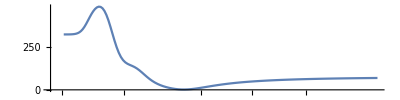

```mathematica
tstart=AbsoluteTime[];j=0;Label[jloop];j=j+1;Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[sinusoidmodel[{P,τ,A1,A2,Pgrid[[j]]},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];bartab={{Pglob,τglob,0,0}};minnyK=NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];Subscript[α, j]={minnyK[[1]],1440 √(minnyK[[2]][[All,2]][[3]]^2+minnyK[[2]][[All,2]][[4]]^2)};If[j<Length[Pgrid],Goto[jloop]];tend=AbsoluteTime[];timeperLS=tend-tstart;
lombscargleK=Table[{Pgrid[[jj]],χ2nullK-Subscript[α, jj][[1]],Subscript[α, jj][[2]]},{jj,1,Length[Pgrid]}];
ListLogLinearPlot[lombscargleK[[All,{1,2}]],PlotRange->All,Joined->True,AspectRatio->0.25]
```

```mathematica
bestPK=Select[lombscargleK,#[[2]]==Max[lombscargleK[[All,2]]]&]
bestΔχ2K=bestPK[[1]][[2]]
bestAK=bestPK[[1]][[3]]
bestPK=bestPK[[1]][[1]]
bestΔBICK=bestΔχ2K-3 Log[Length[TTVsK]]
```

{{2.54417,480.747,6.70202}}

480.747

6.70202

2.54417

474.155

```mathematica
Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[sinusoidmodel[{P,τ,A1,A2,bestPK},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];bartab={{Pglob,τglob,0,0}};minnyK=NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];
bestθK=minnyK[[2]][[All,2]]
bestsinusoidK[t_]:=bestθK[[1]] t+bestθK[[2]]+bestθK[[3]] Sin[(2π t)/bestPK]+bestθK[[4]] Cos[(2π t)/bestPK];
```

{160.884,55110.5,-0.00465184,-0.000147457}

### M first

```mathematica
"define properties of the LS periodogram";
temp=Sort[TTVsM];
minP=2Min[Table[temp[[i+1,1]]-temp[[i,1]],{i,1,Length[temp]-1}]];
maxP=2(Max[temp[[All,1]]]-Min[temp[[All,1]]]);
minν=1/maxP;maxν=1/minP;
ngrid=10Length[temp];
νgrid=N[Table[ν,{ν,minν,maxν,(maxν-minν)/ngrid}]][[1;;ngrid]];
Pgrid=Table[1/νgrid[[i]],{i,1,Length[νgrid]}];
```

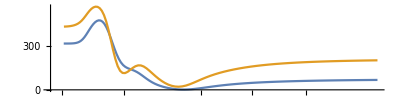

```mathematica
j=0;Label[jloop];j=j+1;Clear[testfnM];testfnM[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[sinusoidmodel[{P,τ,A1,A2,Pgrid[[j]]},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];bartab={{Pglob,τglob,0,0}};minnyM=NMinimize[{testfnM[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];Subscript[α, j]={minnyM[[1]],1440 √(minnyM[[2]][[All,2]][[3]]^2+minnyM[[2]][[All,2]][[4]]^2)};If[j<Length[Pgrid],Goto[jloop]];
lombscargleM=Table[{Pgrid[[jj]],χ2nullM-Subscript[α, jj][[1]],Subscript[α, jj][[2]]},{jj,1,Length[Pgrid]}];
ListLogLinearPlot[{lombscargleK[[All,{1,2}]],lombscargleM[[All,{1,2}]]},PlotRange->All,Joined->True,AspectRatio->0.25]
```

```mathematica
bestPM=Select[lombscargleM,#[[2]]==Max[lombscargleM[[All,2]]]&]
bestΔχ2M=bestPM[[1]][[2]]
bestAM=bestPM[[1]][[3]]
bestPM=bestPM[[1]][[1]]
bestΔBICM=bestΔχ2M-3 Log[Length[TTVsM]]
```

{{2.49027,575.413,7.50301}}

575.413

7.50301

2.49027

569.175

```mathematica
Clear[testfnM];testfnM[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[sinusoidmodel[{P,τ,A1,A2,bestPM},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];bartab={{Pglob,τglob,0,0}};minnyM=NMinimize[{testfnM[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];
bestθM=minnyM[[2]][[All,2]]
bestsinusoidM[t_]:=bestθM[[1]] t+bestθM[[2]]+bestθM[[3]] Sin[(2π t)/bestPM]+bestθM[[4]] Cos[(2π t)/bestPM];
```

{160.885,55110.5,-0.00507119,0.0011965}

### PLOT THE RESULTS

```mathematica
N[3 Log[Length[TTVsK]]]
```

6.59167

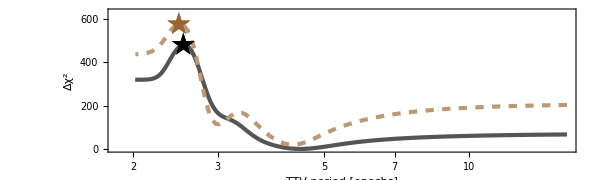

```mathematica
Yrange={0,1.1Max[Max[lombscargleK[[All,2]]],Max[lombscargleM[[All,2]]]]};
tempK={{bestPK,bestΔχ2K}};
tempM={{bestPM,bestΔχ2M}};
LSplot=Show[ListLogLinearPlot[lombscargleK[[All,{1,2}]],PlotRange->{All,Yrange},Frame->True,FrameLabel->{"TTV period [epochs]","Δχ^2"},AspectRatio->0.3,Joined->True,PlotStyle->Directive[Lighter[Black],Thickness[0.005]],ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None],ListLogLinearPlot[lombscargleM[[All,{1,2}]],PlotRange->All,Frame->True,FrameLabel->{"TTV period [epochs]","Δχ^2"},AspectRatio->0.3,Joined->True,PlotStyle->Directive[Lighter[Brown],Dashing[0.01],Thickness[0.005]],ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None],ListLogLinearPlot[tempK,PlotMarkers->{"★",25},PlotStyle->Black],ListLogLinearPlot[tempM,PlotMarkers->{"★",25},PlotStyle->Brown]]
```

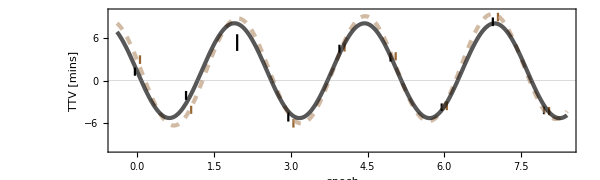

```mathematica
finalttvplot=Show[dataplot,Plot[1440(bestsinusoidM[t]-linearmodel[{Pglob,τglob},t]),{t,xrange[[1]],xrange[[2]]},PlotStyle->Directive[Lighter[Brown],Thickness[0.005],Dashing[0.01],Opacity[0.66]]],Plot[1440(bestsinusoidK[t]-linearmodel[{Pglob,τglob},t]),{t,xrange[[1]],xrange[[2]]},PlotStyle->Directive[Black,Thickness[0.005],Opacity[0.66]]]]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"periodogram.pdf"],LSplot]
Export[StringJoin[NotebookDirectory[],"TTVs.pdf"],finalttvplot]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/periodogram.pdf

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Undersampled/NEWLIGHT1/KOI-3678.01/fits_with3/TTVs.pdf

### Moon times

```mathematica
moontimes={55110.5053980755,55271.387750126465,55432.27927184613,55593.154983394976,55754.0458671042,55914.92908921068,56075.80890208772,56236.70173781406,56397.57792229926};
moontimes=Table[{Round[(moontimes[[i]]-τglob)/Pglob],1440(moontimes[[i]]-Pglob Round[(moontimes[[i]]-τglob)/Pglob]-τglob)},{i,1,Length[moontimes]}]
```

{{0,0.92747},{1,-2.12989},{2,8.01707},{3,-4.60262},{4,4.62561},{5,2.82112},{6,-3.89265},{7,8.14648},{8,-3.79218}}

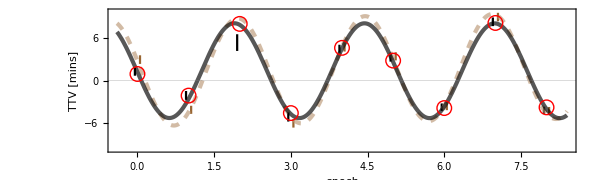

```mathematica
Show[finalttvplot,ListPlot[moontimes,PlotMarkers->{"○",15},PlotStyle->Red]]
```

```mathematica
moontimes
```

{{0,0.92747},{1,-2.12989},{2,8.01707},{3,-4.60262},{4,4.62561},{5,2.82112},{6,-3.89265},{7,8.14648},{8,-3.79218}}

```mathematica
Sum[((TTVsK[[i,3]]-moontimes[[i,2]])/(0.5(TTVsK[[i,4]]+TTVsK[[i,5]])))^2,{i,1,Length[moontimes]}]
```

7.43559

```mathematica
Length[moontimes]
```

9

```mathematica
TTVsK
```

{{0,55110.505629419698,1.26060523,0.576107347,0.57333541},{1,55271.387770393267,-2.10070892,0.629766866,0.624199313},{2,55432.277438814803,5.377502001,1.18964725,1.17331445},{3,55593.154621107649,-5.124312391,0.677682435,0.658677203},{4,55754.045764003997,4.477142258,0.570745905,0.589133831},{5,55914.929415512575,3.29099852,0.608363666,0.610250139},{6,56075.808992183374,-3.762911621,0.51999828,0.523939629},{7,56236.701852831859,8.312106105,0.610963512,0.61276383},{8,56397.577616839102,-4.232039556,0.527316991,0.523194299}}

```mathematica
crossK=Select[TTVsK,MemberQ[TTVsM[[All,1]],#[[1]]]&];
crossM=Select[TTVsM,MemberQ[TTVsK[[All,1]],#[[1]]]&];
Length[crossM]==Length[crossK]
ratioKtoM=((crossK[[All,4]]+crossK[[All,5]])0.5)/((crossM[[All,4]]+crossM[[All,5]])0.5)
```

True

{0.942166,1.09997,1.11363,0.966566,1.05053,0.855687,1.01977,0.905613}

## Cross validation

```mathematica
input=RandomSample[TTVsK,Length[TTVsK]];
nholdout=Round[Length[TTVsK]0.2];
holdout=input[[Length[input]-nholdout+1;;Length[input],All]];
input=input[[1;;Length[input]-nholdout,All]];
Length[holdout]+Length[input]==Length[TTVsK]
```

True

```mathematica
Length[TTVsK]
```

9

```mathematica
nholdout
```

2

```mathematica
Binomial[Length[TTVsK],nholdout]
```

36

```mathematica
z=0;m=0;zmax=400;tstart=AbsoluteTime[];Label[zloop];z=z+1;input=RandomSample[TTVsK,Length[TTVsK]];nholdout=Round[Length[TTVsK]0.2];holdout=input[[Length[input]-nholdout+1;;Length[input],All]];input=input[[1;;Length[input]-nholdout,All]];testfnKlin[P_,τ_]:=χ2fn[Table[{input[[i,2]],N[input[[i,4]]/1440],N[input[[i,5]]/1440]},{i,1,Length[input]}],Table[sinusoidmodel[{P,τ,0,0,Pgrid[[j]]},input[[i,1]]],{i,1,Length[input]}]];bartablin={{Pglob,τglob}};minnyKlin=NMinimize[{testfnKlin[P,τ],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ},Method->{"NelderMead","InitialPoints"->bartablin}];j=0;Label[jloop];j=j+1;Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{input[[i,2]],N[input[[i,4]]/1440],N[input[[i,5]]/1440]},{i,1,Length[input]}],Table[sinusoidmodel[{P,τ,A1,A2,Pgrid[[j]]},input[[i,1]]],{i,1,Length[input]}]];bartab={{Pglob,τglob,0,0}};minnyK=NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];Subscript[α, j]=minnyK[[1]];If[j<Length[Pgrid],Goto[jloop]];bestsol=Sort[Table[{Pgrid[[jj]],Subscript[α, jj]},{jj,1,Length[Pgrid]}],#1[[2]]<#2[[2]]&][[1]];Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{input[[i,2]],N[input[[i,4]]/1440],N[input[[i,5]]/1440]},{i,1,Length[input]}],Table[sinusoidmodel[{P,τ,A1,A2,bestsol[[1]]},input[[i,1]]],{i,1,Length[input]}]];bestminny=Last[NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}]][[All,2]];holdoutprediction=Table[sinusoidmodel[{bestminny[[1]],bestminny[[2]],bestminny[[3]],bestminny[[4]],bestsol[[1]]},holdout[[i,1]]],{i,1,Length[holdout]}];holdoutprediction=Table[sinusoidmodel[{bestminny[[1]],bestminny[[2]],bestminny[[3]],bestminny[[4]],bestsol[[1]]},holdout[[i,1]]],{i,1,Length[holdout]}];χ2sin=χ2fn[Table[{holdout[[i,2]],N[holdout[[i,4]]/1440],N[holdout[[i,5]]/1440]},{i,1,Length[holdout]}],holdoutprediction];holdoutpredictionlin=Table[sinusoidmodel[{Last[minnyKlin][[All,2]][[1]],Last[minnyKlin][[All,2]][[2]],0,0,bestsol[[1]]},holdout[[i,1]]],{i,1,Length[holdout]}];χ2lin=χ2fn[Table[{holdout[[i,2]],N[holdout[[i,4]]/1440],N[holdout[[i,5]]/1440]},{i,1,Length[holdout]}],holdoutpredictionlin];If[χ2sin<χ2lin,m=m+1];If[z<zmax,Goto[zloop]];tend=AbsoluteTime[];
tend-tstart
```

36630.15441

```mathematica
m
```

391

```mathematica
(10*3600)/90
```

400